The internal dynamics f: R^3 to R^3 is the Lorenz Equations.
This notebook makes pdfs for Figure 5 in “Invariant Synchrony and Anti-Synchrony Subspaces of Weighted Networks”, by Niholt, Sieben and Swift.

```mathematica
SetDirectory["C:\\Users\\jws8\\Dropbox\\Conjecture5.3\\Article\\Version 1\\"] (* Jim's office machine.  The figures look slightly different with the different machines due to Lorenz equation chaos *)
f[{u_, v_, w_}] := {10(v-u),u(28-w) -v, u v - 8/3 w} (* Lorenz equations *)
H11 = {{1,0, 0},{0,0,0},{0,0,0}};
H12 = {{0,1, 0},{0,0,0},{0,0,0}};
H13 = {{0,0, 1},{0,0,0},{0,0,0}};
H21 = {{0,0, 0},{1,0,0},{0,0,0}};
H22 = {{0,0, 0},{0,1,0},{0,0,0}};
H23 = {{0,0, 0},{0,0,1},{0,0,0}};
H31 = {{0,0, 0},{0,0,0},{1,0,0}};
H32 = {{0,0, 0},{0,0,0},{0,1,0}};
H33 = {{0,0, 0},{0,0,0},{0,0,1}};
NLorenz = {{-1,0,0},{0,-1,0}, {0,0,1}};
H = H33;
Ht = Transpose[H];
Clear[x];
x[t_] :={{x11[t],x12[t], x13[t]}, {x21[t],x22[t], x23[t]}}
u1u2[x_] := {x[[1,1]], x[[2,1]]}  (* The schematic "y" function.  Output a list {u1, u2} to plot *)
w1w2[x_] := {x[[1,3]], x[[2,3]]}  (* The schematic "y" function.  Output a list {w1, w2} to plot *)
 uwSumDif[x_] := {x[[1,1]]+x[[2,1]], x[[1,3]]- x[[2,3]]} (* {u1 - u2 and w1 + w2} plotted. This is {0,0} on the anti-synchrony solution. *)
κ =-2;  
L =  {{1,-1},{-1,1}};
M = κ L;

printInfo := Module[{},
Print["x' = f[x] + M.x.H^T, f[u,v,w] = ", f[{u,v, w}]];
Print["M = ", κ,MatrixForm[Chop[M/κ]], ", H = ", MatrixForm[H]];
]
myPlotStyle ={{Red}, {Blue,  Dashed}};
myPlotRange ={-20,20};
myPlotRange = All;
```

C:\Users\jws8\Dropbox\Conjecture5.3\Article\Version 1

```mathematica
myseed =2;
SeedRandom[myseed];
x0a = RandomReal[{-10, 10}, {2,3}]
x0b = {x0a[[1]], NLorenz.x0a[[2]]}
```

{{4.4448,-7.81103,-0.585946},{0.711637,1.66355,-4.12115}}

{{4.4448,-7.81103,-0.585946},{-0.711637,-1.66355,-4.12115}}

x' = f[x] + M.x.H^T, f[u,v,w] = {10 (-u+v),-v+u (28-w),u v-(8 w)/3}

M = -2(1 | -1
-1 | 1), H = (0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

First row seed = 2, x[0] = {{4.4448,-7.81103,-0.585946},{0.711637,1.66355,-4.12115}}

300

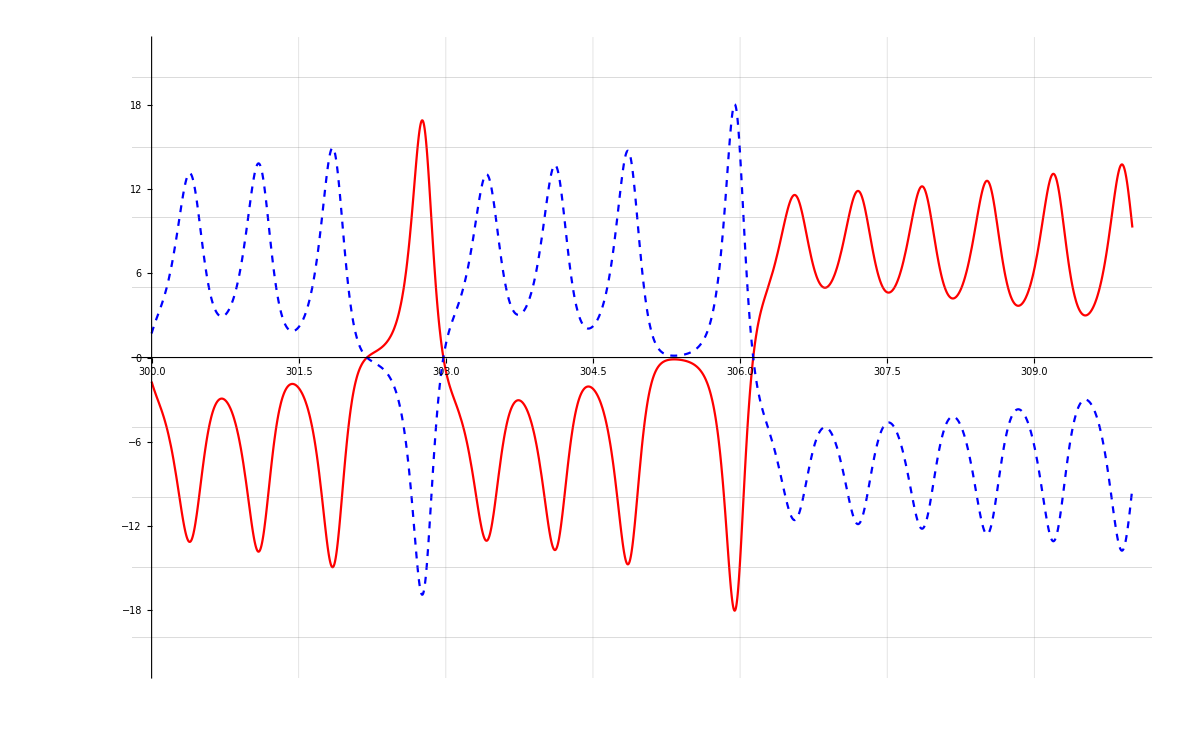

Second row x[0] = {{4.4448,-7.81103,-0.585946},{-0.711637,-1.66355,-4.12115}}

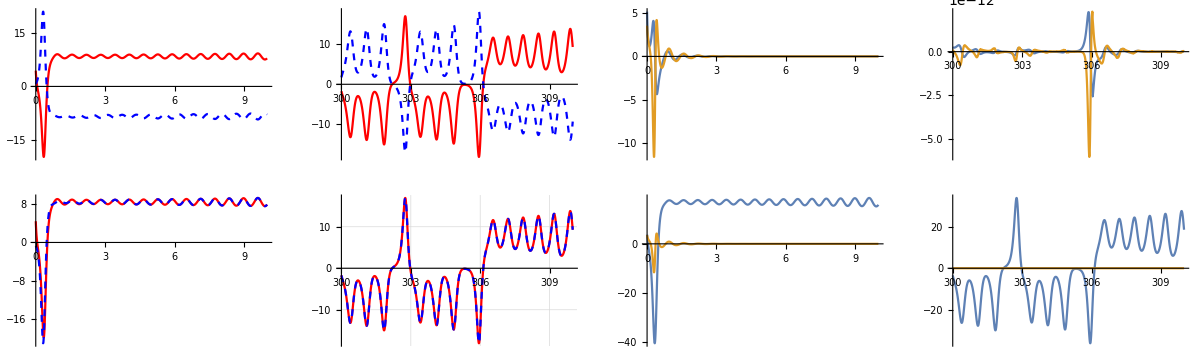

```mathematica
ode = x'[t] ==  Map[f, x[t]]  +  M.x[t].Ht;
printInfo

x0 = x0a;
ic = x[0] ==  x0;
Print["First row seed = ", myseed, ", x[0] = ", x0]
ivp = LogicalExpand[ode&& ic];
tPlot = 10;
tTransient =300
tMax = tTransient + tPlot;
s = NDSolve[ivp, x[t], {t, 0, tMax}][[1]]; (* s is the first and only solution *)
paInit = Plot[Evaluate[u1u2[x[t]/.s]], {t, 0, tPlot}, PlotStyle -> myPlotStyle, PlotRange -> All];
paAfterTransient = Plot[Evaluate[u1u2[x[t]/.s]], {t, tTransient, tMax}, PlotStyle -> myPlotStyle, PlotRange -> myPlotRange];
paSumDifInit = Plot[Evaluate[uwSumDif[x[t]/.s]], {t, 0, tPlot}, PlotRange -> myPlotRange];
paSumDifAfterTransient = Plot[Evaluate[uwSumDif[x[t]/.s]], {t, tTransient, tMax}, PlotRange -> myPlotRange];

If[H==H22 && κ == 2  && myseed == 3 &&True, (* We don't want to over-write by mistake. The seed of 3 gives a nice starting point in the plot *)
pH22K2 = Plot[Evaluate[u1u2[x[t]/.s]], {t, tTransient, tMax}, PlotStyle -> myPlotStyle, PlotRange -> {-22,22}, GridLines ->{Automatic,Range[-20, 20, 5]}];
Export["pH22K2.pdf",pH22K2, ImageSize-> 350];
Show[pH22K2]
]
If[H==H33 && κ == -2  && myseed == 2 &&True, (* We don't want to over-write by mistake. Seeds 0, 3, 4, 6, etc give ((a,b,c),(a,b,c)), seeds 1, 2, 5, etc give ((a,b,c),(-a,-b,c) *)
pH33Km2 = Plot[Evaluate[u1u2[x[t]/.s]], {t, tTransient, tMax}, PlotStyle -> myPlotStyle, PlotRange -> {-22,22}, GridLines ->{Automatic,Range[-20, 20, 5]}];
Export["pH33Km2.pdf",pH33Km2, ImageSize-> 350];
Show[pH33Km2]
]

x0 = x0b;
ic = x[0] ==  x0;
Print["Second row x[0] = ", x0]
ivp = LogicalExpand[ode&& ic];
s = NDSolve[ivp, x[t], {t, 0, tMax}][[1]]; (* s is the first and only solution *)
pbInit = Plot[Evaluate[u1u2[x[t]/.s]], {t, 0, tPlot}, PlotStyle -> myPlotStyle, PlotRange -> All];
pbAfterTransient = Plot[Evaluate[u1u2[x[t]/.s]], {t, tTransient, tMax}, PlotStyle -> myPlotStyle, PlotRange -> myPlotRange, GridLines -> Automatic];
pbSumDifInit = Plot[Evaluate[uwSumDif[x[t]/.s]], {t, 0, tPlot}, PlotRange -> myPlotRange];
pbSumDifAfterTransient = Plot[Evaluate[uwSumDif[x[t]/.s]], {t, tTransient, tMax}, PlotRange -> myPlotRange];

GraphicsGrid[{{paInit, paAfterTransient, paSumDifInit,paSumDifAfterTransient},{pbInit, pbAfterTransient,pbSumDifInit,pbSumDifAfterTransient}}, ImageSize -> 1200]
```